New in CIP 1.1

Entering Non-Linearity with Multiple Polynomial Regression (MPR)

This tutorial demonstrates new functions of CIP version 1.1 that complement the discussion in textbook

Achim Zielesny, From Curve Fitting to Machine Learning: An illustrative Guide to scientific Data Analysis and Computational Intelligence, Berlin 2011. (Springer: Intelligent Systems Reference Library, Volume 18).

CIP is available at http://www.gnwi.de.

```mathematica
Clear["Global`*"];
<<CIP`ExperimentalData`
<<CIP`Graphics`
<<CIP`MPR`
```

A model function for an experimental adhesive kinetics data set is approximated: The experimental data describe the dependence of a kinetics parameter on the composition of an adhesive polymer mixture. The adhesive kinetics data set is provided by the CIP ExperimentalData package:

```mathematica
dataSet=CIP`ExperimentalData`GetAdhesiveKineticsDataSet[];
CIP`Graphics`ShowDataSetInfo[{"IoPairs","InputComponents","OutputComponents"},dataSet]
```

Number of IO pairs = 73

Number of input components = 3

Number of output components = 1

The data set contains 73 I/O pairs where each I/O pair is four-dimensional (inputs with three components, outputs with one component) so the complete data set can not be displayed with 2D or 3D graphics. But due to the experimental measurement setup it is possible to obtain subsets of data that are suitable for visual inspection in 3D. The experimental errors of the data are reported to be in the order of 10% to 20% with some outliers which is an essential information for the assessment of the goodness of regression in the following. The modelling task is approached with the application of multiple linear regression (MLR), i.e. a polynomial order of 1 for multiple polynomial regression (MPR).

```mathematica
polynomialOrder=1;
```

A fit of the data set with MLR (i.e. MPR with a polynomial order of 1) tries to estimate 4 model parameters

```mathematica
CIP`MPR`GetMprNumberOfParameters[dataSet,polynomialOrder]
```

4

and leads to a regression result

```mathematica
mprInfo=CIP`MPR`FitMpr[dataSet,polynomialOrder];
```

with obvious systematic deviations between data and model (positive deviations for small and large output values and negative deviations in between) as is illustrated by the model-versus-data and relative residuals plot:

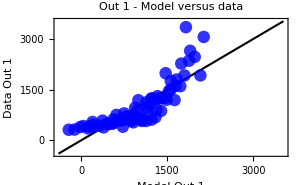

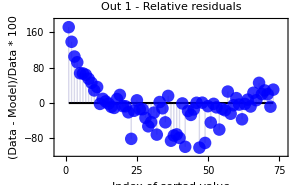

```mathematica
CIP`MPR`ShowMprSingleRegression[{"ModelVsDataPlot","RelativeSortedResidualsPlot"},dataSet,mprInfo];
```

The relative residuals statistics

```mathematica
CIP`MPR`ShowMprSingleRegression[{"RelativeResidualsStatistics","CorrelationCoefficient"},dataSet,mprInfo];
```

Definition of 'Residual (percent)': 100*(Data - Model)/Data

Out 1 : Residual (percent): Mean/Median/Maximum Value = 3.44×10^1 / 2.02×10^1 / 1.71×10^2

Out 1 : Correlation coefficient = 0.840707

show that the magnitude of the deviations (over 30% on average) is obviously above the reported experimental errors of 10 to 20% and the correlation coefficient is poor in addition. So it can be deduced that the adhesive kinetics data can not be satisfactorily modelled by MLR. This may also be illustrated by the 3D display of a subset of the data that corresponds to a specific polymer mass ratio of the mixture:

```mathematica
polymerMassRatio="80";
dataSet3D=CIP`ExperimentalData`GetAdhesiveKinetics3dDataSet[polymerMassRatio];
indexOfInput1=2;
indexOfInput2=3;
indexOfOutput=1;
input={80.0,0.0,0.0};
pureMpr3dFunction=Function[{x,y},CIP`MPR`CalculateMpr3dValue[x,y,indexOfInput1,indexOfInput2,indexOfOutput,input,mprInfo]];
labels={"In 2","In 3","Out 1"};
CIP`Graphics`Plot3dDataSetWithFunction[dataSet3D,pureMpr3dFunction,labels]
```

-Graphics3D-

The linear plane is only a poor approximate description of the data. On the other hand the adhesive kinetics data are not dramatically non-linear - the true relation seems to be a slightly curved surface. Thus the MLR approach is slightly extended into the non-linear region by an a priori/a posterior data transformation with logarithmic/exponential function: The output components are transformed by a logarithmic function before the MLR fit, the function values of the MLR generated model functions are then afterwards inversely transformed by a exponential function (see the CIP code for details). Here are the results for the logarithmic/exponential transformation:

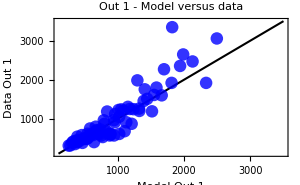

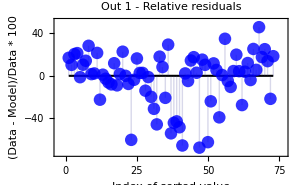

Definition of 'Residual (percent)': 100*(Data - Model)/Data

Out 1 : Residual (percent): Mean/Median/Maximum Value = 1.84×10^1 / 1.41×10^1 / 6.74×10^1

Out 1 : Correlation coefficient = 0.912715

```mathematica
dataTransformationMode="Log";
mprInfo=CIP`MPR`FitMpr[dataSet,polynomialOrder,MprOptionDataTransformationMode->dataTransformationMode];
CIP`MPR`ShowMprSingleRegression[{"ModelVsDataPlot","RelativeSortedResidualsPlot","RelativeResidualsStatistics","CorrelationCoefficient"},dataSet,mprInfo];
```

The systematic deviations between data and model are now confined to the larger output value region and the residuals statistics are more acceptable with a value around 18% on average. Also the correlation coefficient increased. The 3D plot of the subset of data with the approximated model function

```mathematica
pureMpr3dFunction=Function[{x,y},CIP`MPR`CalculateMpr3dValue[x,y,indexOfInput1,indexOfInput2,indexOfOutput,input,mprInfo]];
CIP`Graphics`Plot3dDataSetWithFunction[dataSet3D,pureMpr3dFunction,labels]
```

-Graphics3D-

demonstrates the improvement. The adhesive kinetics data seem to be at the borderline for a successful application of a non-linear enhanced MLR approach. To further improve the modelling result a switch to non-linear machine learning methods is necessary with the polynomial expansion as a first step. If a general quadratic polynomial (i.e. a polynomial order of 2) is chosen

```mathematica
polynomialOrder=2;
CIP`MPR`GetMprNumberOfParameters[dataSet,polynomialOrder]
```

10

the model now contains 10 parameters to be estimated. Compared to pure MLR the polynomial expansion leads to a clear improvement:

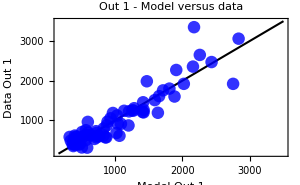

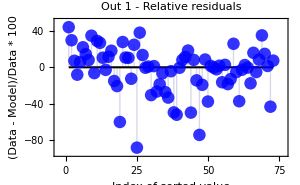

Definition of 'Residual (percent)': 100*(Data - Model)/Data

Out 1 : Residual (percent): Mean/Median/Maximum Value = 1.9×10^1 / 1.44×10^1 / 8.85×10^1

Out 1 : Correlation coefficient = 0.92732

```mathematica
mprInfo=CIP`MPR`FitMpr[dataSet,polynomialOrder];
CIP`MPR`ShowMprSingleRegression[{"ModelVsDataPlot","RelativeSortedResidualsPlot","RelativeResidualsStatistics","CorrelationCoefficient"},dataSet,mprInfo];
```

The systematic deviations are less pronounced and the residuals are at the upper experimental limit. The improvement is also directly visible by the 3D plot of the sub set of data:

```mathematica
pureMpr3dFunction=Function[{x,y},CIP`MPR`CalculateMpr3dValue[x,y,indexOfInput1,indexOfInput2,indexOfOutput,input,mprInfo]];
CIP`Graphics`Plot3dDataSetWithFunction[dataSet3D,pureMpr3dFunction,labels]
```

-Graphics3D-

An additional logarithmic/exponential transformation

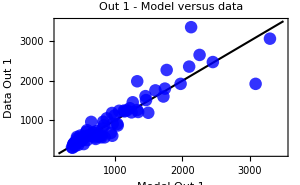

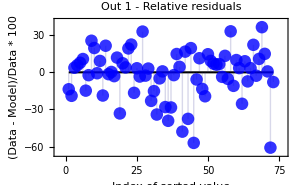

Definition of 'Residual (percent)': 100*(Data - Model)/Data

Out 1 : Residual (percent): Mean/Median/Maximum Value = 1.49×10^1 / 1.09×10^1 / 6.08×10^1

Out 1 : Correlation coefficient = 0.921525

```mathematica
mprInfo=CIP`MPR`FitMpr[dataSet,polynomialOrder,MprOptionDataTransformationMode->dataTransformationMode];
CIP`MPR`ShowMprSingleRegression[{"ModelVsDataPlot","RelativeSortedResidualsPlot","RelativeResidualsStatistics","CorrelationCoefficient"},dataSet,mprInfo];
```

leads to an overall satisfying result:

```mathematica
pureMpr3dFunction=Function[{x,y},CIP`MPR`CalculateMpr3dValue[x,y,indexOfInput1,indexOfInput2,indexOfOutput,input,mprInfo]];
quadraticLogGraphics3D=CIP`Graphics`Plot3dDataSetWithFunction[dataSet3D,pureMpr3dFunction,labels]
```

-Graphics3D-

If the polynomial order is further expanded in the cubic region

```mathematica
polynomialOrder=3;
CIP`MPR`GetMprNumberOfParameters[dataSet,polynomialOrder]
```

20

the model consists of 20 parameters to be estimated. The cubic MPR fit

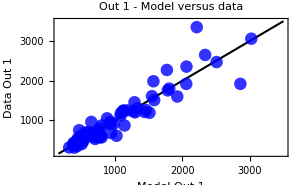

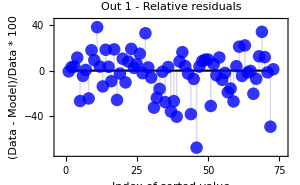

Definition of 'Residual (percent)': 100*(Data - Model)/Data

Out 1 : Residual (percent): Mean/Median/Maximum Value = 1.43×10^1 / 9.75 / 6.73×10^1

Out 1 : Correlation coefficient = 0.936048

```mathematica
mprInfo=CIP`MPR`FitMpr[dataSet,polynomialOrder];
CIP`MPR`ShowMprSingleRegression[{"ModelVsDataPlot","RelativeSortedResidualsPlot","RelativeResidualsStatistics","CorrelationCoefficient"},dataSet,mprInfo];
```

```mathematica
pureMpr3dFunction=Function[{x,y},CIP`MPR`CalculateMpr3dValue[x,y,indexOfInput1,indexOfInput2,indexOfOutput,input,mprInfo]];
cubicGraphics3D=CIP`Graphics`Plot3dDataSetWithFunction[dataSet3D,pureMpr3dFunction,labels]
```

-Graphics3D-

directly achieves a satisfying result (maybe with a slight overfitted buckle). An additional logarithmic/exponential transformation

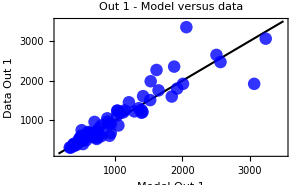

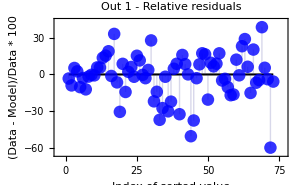

Definition of 'Residual (percent)': 100*(Data - Model)/Data

Out 1 : Residual (percent): Mean/Median/Maximum Value = 1.34×10^1 / 8.93 / 5.97×10^1

Out 1 : Correlation coefficient = 0.921784

```mathematica
mprInfo=CIP`MPR`FitMpr[dataSet,polynomialOrder,MprOptionDataTransformationMode->dataTransformationMode];
CIP`MPR`ShowMprSingleRegression[{"ModelVsDataPlot","RelativeSortedResidualsPlot","RelativeResidualsStatistics","CorrelationCoefficient"},dataSet,mprInfo];
```

```mathematica
pureMpr3dFunction=Function[{x,y},CIP`MPR`CalculateMpr3dValue[x,y,indexOfInput1,indexOfInput2,indexOfOutput,input,mprInfo]];
cubicLogGraphics3D=CIP`Graphics`Plot3dDataSetWithFunction[dataSet3D,pureMpr3dFunction,labels]
```

-Graphics3D-

does not lead to a significantly improved model (but seems to smooth the buckle a bit). An overlay of the last results (quadratic-log, cubic and cubic-log)

```mathematica
Show[quadraticLogGraphics3D,cubicGraphics3D,cubicLogGraphics3D]
```

-Graphics3D-

show that they all adequately fit the data. The one to choose for a predictive interpolation task is thus a mere matter of taste. The models are probably the best we can get for the adhesive kinetics modelling problem - and they are convincing and helpful to the adhesive scientists. Note that the increase of the polynomial order (polynomially) increases the number of model related parameters to be estimated by the fitting procedure but allows the model function to be more non-linearly curved. This may lead to an unwanted overfitting of the data as may be illustrated with a polynomial order of 6 for the current regression task:

```mathematica
polynomialOrder=6;
CIP`MPR`GetMprNumberOfParameters[dataSet,polynomialOrder]
```

84

The number of model parameters now exceeds the number of I/O pairs in the data set and the corresponding MPR fit

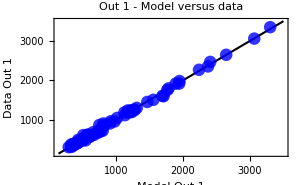

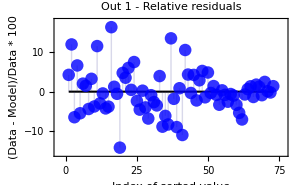

Definition of 'Residual (percent)': 100*(Data - Model)/Data

Out 1 : Residual (percent): Mean/Median/Maximum Value = 3.97 / 3.24 / 1.63×10^1

Out 1 : Correlation coefficient = 0.998134

```mathematica
mprInfo=CIP`MPR`FitMpr[dataSet,polynomialOrder];
CIP`MPR`ShowMprSingleRegression[{"ModelVsDataPlot","RelativeSortedResidualsPlot","RelativeResidualsStatistics","CorrelationCoefficient"},dataSet,mprInfo];
```

leads to a perfect description of the data (i.e. a kind of look-up table) but to an unwanted overfitted model without predictability:

```mathematica
pureMpr3dFunction=Function[{x,y},CIP`MPR`CalculateMpr3dValue[x,y,indexOfInput1,indexOfInput2,indexOfOutput,input,mprInfo]];
CIP`Graphics`Plot3dDataSetWithFunction[dataSet3D,pureMpr3dFunction,labels]
```

-Graphics3D-

Finally note that the correlation coefficient can indicate a better model but a higher value may also mean undesired overfitting as demonstrated by the last fitting result with a value to be practically 1 (for perfect correlation).